### Base

Set the Census API key

```mathematica
(*SystemCredential["USCensusAPIKey"]="your Census API key"*)
```

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse,responseList},
rawResponse=Confirm@URLRead@HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>];
responseList=Confirm@Import[rawResponse,"RawJSON"];
ToTabular[Rest@responseList,"Rows",<|"ColumnKeys"->First@responseList|>]
]
```

### PUMS

https://www.census.gov/data/developers/data-sets/census-microdata-api.ACS_5-Year_PUMS.html

Variable interpretations: https://api.census.gov/data/2022/acs/acs5/pums/variables/CIT.json

Information on handling weights: https://www.census.gov/content/dam/Census/library/publications/2020/acs/acs_pums_handbook_2020_ch04.pdf

```mathematica
georgiaPUMSRaw=censusQuery[
{"data","2022","acs","acs5","pums"},
{
"get"->StringRiffle[{"PWGTP","CIT","AGEP","HISP","RACWHT","RACBLK","RACASN","RACAIAN","RACNH","RACPI","RACSOR","RACNUM"},","],
"for"->"state:"<>Entity["AdministrativeDivision",{"Georgia","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]],
(*"for"->"public use microdata area:00500"*)
}
];//EchoTiming
```

35.9705

```mathematica
georgiaPUMS=ConstructColumns[georgiaPUMSRaw,
{
"PersonWeight"->Function[Cast[#PWGTP,"UnsignedInteger16"]],
"Age"->Function[Cast[#AGEP,"UnsignedInteger8"]],
"Citizen"->Function[#CIT=!="5"],
"HispanicOrLatino"->Function[#HISP=!="01"],
"White"->Function[#RACWHT==="1"],
"BlackOrAfricanAmerican"->Function[#RACBLK==="1"],
"Asian"->Function[#RACASN==="1"],
"AmericanIndianAndAlaskaNative"->Function[#RACAIAN==="1"],
"NativeHawaiianAndOtherPacificIslander"->Function[#RACNH==="1"||#RACPI==="1"],(*PUMS splits only this category into two variables for some reason*)
"SomeOtherRace"->Function[#RACSOR==="1"]
}
];
```

```mathematica
georgiaPUMS
```

Sanity check with the RACNUM variable:

```mathematica
ConstructColumns[georgiaPUMS,
"raceNum"->Function[Total@Boole@Lookup[#,{"White","BlackOrAfricanAmerican","Asian","AmericanIndianAndAlaskaNative","NativeHawaiianAndOtherPacificIslander","SomeOtherRace"}]]
][[All,"raceNum"]]===CastColumns[georgiaPUMSRaw,"RACNUM"->"Integer64"][[All,"RACNUM"]]
```

True

```mathematica
acsCategoryPreds=<|
"WhiteAlone"->Function[#White&&!#BlackOrAfricanAmerican&&!#Asian&&!#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndOtherPacificIslander&&!#SomeOtherRace],
"BlackOrAfricanAmericanAlone"->Function[!#White&&#BlackOrAfricanAmerican&&!#Asian&&!#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndOtherPacificIslander&&!#SomeOtherRace],
"AsianAlone"->Function[!#White&&!#BlackOrAfricanAmerican&&#Asian&&!#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndOtherPacificIslander&&!#SomeOtherRace],
"AmericanIndianAndAlaskaNativeAlone"->Function[!#White&&!#BlackOrAfricanAmerican&&!#Asian&&#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndOtherPacificIslander&&!#SomeOtherRace],
"NativeHawaiianAndOtherPacificIslanderAlone"->Function[!#White&&!#BlackOrAfricanAmerican&&!#Asian&&!#AmericanIndianAndAlaskaNative&&#NativeHawaiianAndOtherPacificIslander&&!#SomeOtherRace],
"SomeOtherRaceAlone"->Function[!#White&&!#BlackOrAfricanAmerican&&!#Asian&&!#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndOtherPacificIslander&&#SomeOtherRace],
"TwoOrMore"->Function[Total@Boole@{#White,#BlackOrAfricanAmerican,#Asian,#AmericanIndianAndAlaskaNative,#NativeHawaiianAndOtherPacificIslander,#SomeOtherRace}>=2],
"HispanicOrLatino"->Function[#HispanicOrLatino],
"WhiteAloneNotHispanicOrLatino"->Function[!#HispanicOrLatino&&#White&&!#BlackOrAfricanAmerican&&!#Asian&&!#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndOtherPacificIslander&&!#SomeOtherRace],
"Overall"->Function[True]
|>;
```

### Comparing to ACS

#### Init

```mathematica
getACSStateRaw[state_,r_,year_:$defaultACSVintage]:=
Module[{rawResponse,rawAcsData,vapVars,cvapVars},
vapVars=Join[getVAPVarsACS[r],getVAPErrorVarsACS[r]];
cvapVars=Join[getCVAPVarsACS[r],getCVAPErrorVarsACS[r]];
rawAcsData=censusQuery[
{"data",year,"acs","acs5"},
{
"get"->StringRiffle[Join[vapVars,cvapVars],","],
"for"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]]
}
];
Map[
c|-><|
{c,"VAP"}->Total@ToExpression@Lookup[#,getVAPVarsACS[c]],
{c,"CVAP"}->Total@ToExpression@Lookup[#,getCVAPVarsACS[c]]
|>,
Flatten[{r}]
]&@First@Normal@rawAcsData
]
getACSState[state_,r_,year_:$defaultACSVintage]:=Merge[BlockMap[getACSStateRaw[state,#,year]&,r,UpTo[4]],Last]
```

#### Experiments

```mathematica
georgiaACSCounts=getACSState[Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],Keys@acsCategories];
```

```mathematica
georgiaACSCounts=;
```

```mathematica
georgiaPUMSCounts=AssociationMap[Apply@Function[{r,c},
Total@Select[georgiaPUMS,acsCategoryPreds[r][#]&&#Age>=18&&If[c==="CVAP",#Citizen,True]&][[All,"PersonWeight"]]],
Keys[georgiaACSCounts]
];
```

The numbers generally line up between the ACS API (detail tables) and PUMS:

```mathematica
Dataset@Merge[{georgiaACSCounts,georgiaPUMSCounts},Identity]
```

```mathematica
ListLogLogPlot[
Merge[{georgiaACSCounts,georgiaPUMSCounts},Identity],
AspectRatio->Automatic,
PlotRange->All,
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
Frame->True,FrameLabel->{"ACS estimate","PUMS estimate"}
]
```

-Graphics-

### Category conversion

```mathematica
LinearSolve
```

```mathematica
Mean@Boole@Select[georgiaPUMS,#BlackOrAfricanAmerican&&!#White&&!#Asian&&!#AmericanIndianAndAlaskaNative&&!#NativeHawaiianAndPacificIslander&&!#SomeOtherRace&][[All,"HispanicOrLatino"]]
```

0.0128393

```mathematica
Select[georgiaPUMS,#BlackOrAfricanAmerican&&#HispanicOrLatino&]
```

### Check that results algin with this weighting scheme

```mathematica
censusQuery[
{"data","2023","acs","acs5","pums"},
{"tabulate"->"weight(PWGTP)","col SEX"->"","row MAR"->"","for"->"public use microdata area:00500","in"->"state:12","SCHL"->"24"}
]
```

### Random socioeconomic experiments

```mathematica
allIncomeRaw=censusQuery[
{"data","2022","acs","acs5","pums"},
{
"get"->StringRiffle[{"WGTP","PWGTP","AGEP","WAGP","PINCP","GRPIP","HINCP"},","],
"for"->"state:*"
}
];//EchoTiming
```

558.063

```mathematica
Beep[]
```

```mathematica
allIncome=CastColumns[
allIncomeRaw,{
"WGTP"->"Integer",
"PWGTP"->"Integer",
"AGEP"->"Integer",
"WAGP"->"Integer",
"PINCP"->"Integer",
"GRPIP"->"Integer",
"HINCP"->"Integer"
}];
```

```mathematica
georgiaIncomeRaw=censusQuery[
{"data","2022","acs","acs5","pums"},
{
"get"->StringRiffle[{"WGTP","PWGTP","AGEP","WAGP","PINCP","GRPIP","HINCP"},","],
"for"->"state:"<>Entity["AdministrativeDivision",{"Georgia","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]]
}
];
```

```mathematica
georgiaIncome=CastColumns[
georgiaIncomeRaw,{
"WGTP"->"Integer",
"PWGTP"->"Integer",
"AGEP"->"Integer",
"WAGP"->"Integer",
"PINCP"->"Integer",
"GRPIP"->"Integer",
"HINCP"->"Integer"
}];
```

```mathematica
incomeWeightedData[t_,v_,w_:"PWGTP"]:=
WeightedData[Normal@t[[All,v]],Normal@t[[All,w]]]
```

```mathematica
incomeWeightedData2[t_,v_,w_:"PWGTP"]:=
Catenate@MapThread[ConstantArray,{Normal@t[[All,v]],Normal@t[[All,w]]}]
```

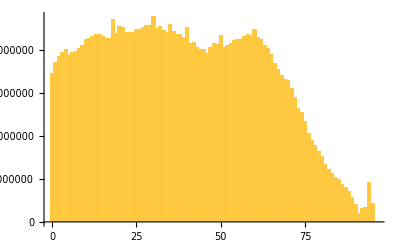

```mathematica
Histogram[incomeWeightedData[allIncome,"AGEP"],{1}]
```

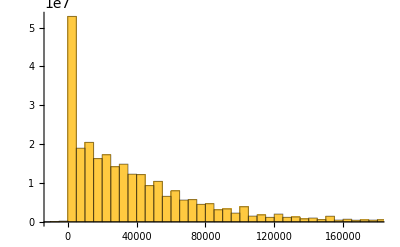

```mathematica
Histogram[incomeWeightedData[Discard[allIncome,#PINCP===-19999&],"PINCP"],{5000}]
```

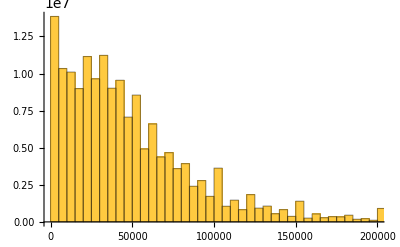

```mathematica
Histogram[incomeWeightedData[Select[allIncome,#WAGP>=4&],"WAGP"],{5000}]
```

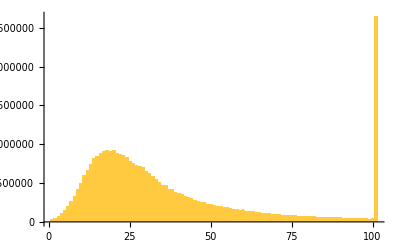

```mathematica
Histogram[incomeWeightedData[Select[allIncome,#GRPIP>0&],"GRPIP"],{1}]
```

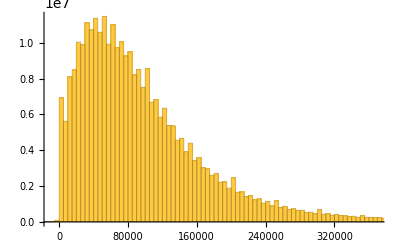

```mathematica
Histogram[incomeWeightedData[Discard[allIncome,#HINCP===-60000&],"HINCP","WGTP"],{5000}]
```

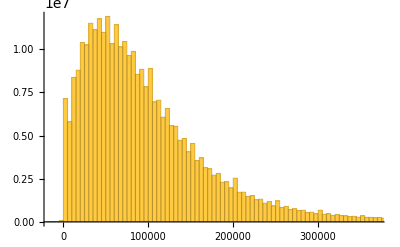

```mathematica
Histogram[incomeWeightedData[Discard[allIncome,#HINCP===-60000&],"HINCP"],{5000}]
```

```mathematica
EstimatedDistribution[N@incomeWeightedData2[Select[allIncome,Positive[#HINCP]&],"HINCP"],LogNormalDistribution[μ,σ]]
```

LogNormalDistribution[11.1989,0.982063]

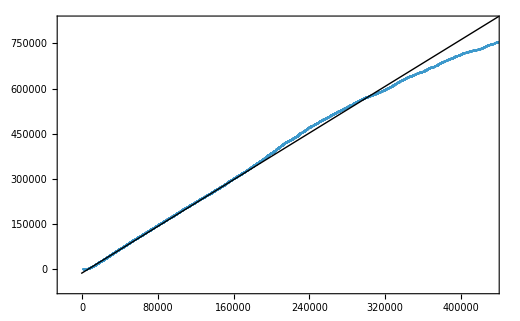

```mathematica
QuantilePlot[
incomeWeightedData[RandomSample[Select[allIncome,Positive[#HINCP]&],100000],"HINCP"],
LogNormalDistribution[11.19885425451784,0.9820625647145426]
]
```

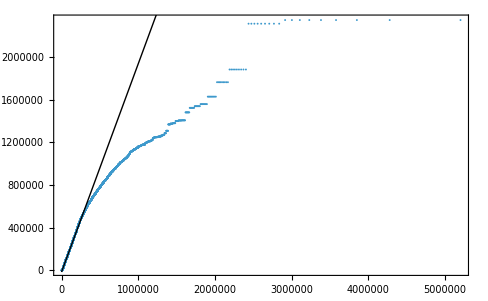

```mathematica
QuantilePlot[
incomeWeightedData[RandomSample[Select[allIncome,Positive[#HINCP]&],100000],"HINCP"],
LogNormalDistribution[11.19885425451784,0.9820625647145426],
PlotRange->All
]
```

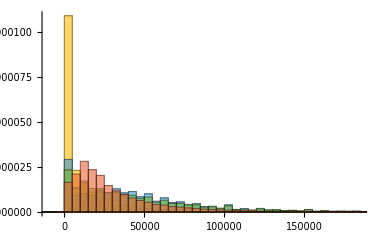

```mathematica
Histogram[
incomeWeightedData[#,"PINCP"]&/@KeySort@GroupBy[Discard[allIncome,#PINCP===-19999&],Floor[#AGEP,25]&],
{5000},
"PDF"
]
```

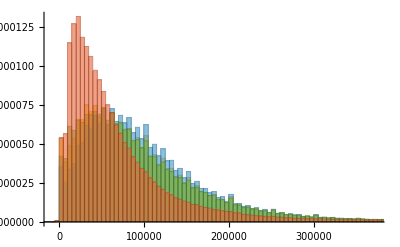

```mathematica
Histogram[
incomeWeightedData[#,"HINCP"]&/@KeySort@GroupBy[Discard[allIncome,#HINCP===-60000&],Floor[#AGEP,25]&],
{5000},
"PDF"
]
```

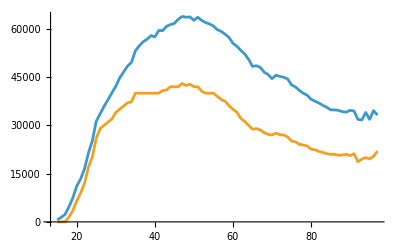

```mathematica
ListLinePlot[
{
KeyValueMap[List,
Mean@incomeWeightedData[#,"PINCP"]&/@KeySort@GroupBy[Discard[allIncome,#PINCP===-19999&],#AGEP&]
],
KeyValueMap[List,
Median@incomeWeightedData[#,"PINCP"]&/@KeySort@GroupBy[Discard[allIncome,#PINCP===-19999&],#AGEP&]
]
},
PlotRange->All
]
```

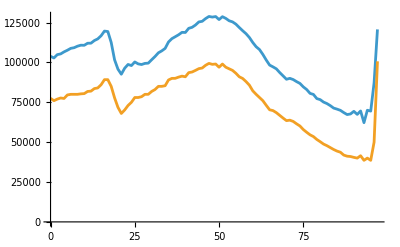

```mathematica
ListLinePlot[
{
KeyValueMap[List,
Mean@incomeWeightedData[#,"HINCP"]&/@KeySort@GroupBy[Discard[allIncome,#HINCP===-60000&],#AGEP&]
],
KeyValueMap[List,
Median@incomeWeightedData[#,"HINCP"]&/@KeySort@GroupBy[Discard[allIncome,#HINCP===-60000&],#AGEP&]
]
},
PlotRange->All
]
```

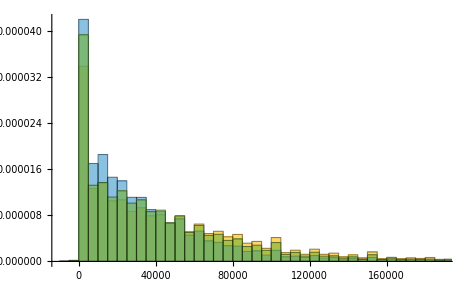

```mathematica
Histogram[
incomeWeightedData[#,"PINCP"]&/@GroupBy[Discard[allIncome,#PINCP===-19999&],#state&][[{
Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]],
Entity["AdministrativeDivision",{"Alabama","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]],
=[Illinois][EntityProperty["AdministrativeDivision","FIPSCode"]]
}]],
{5000},
"PDF"
]
```

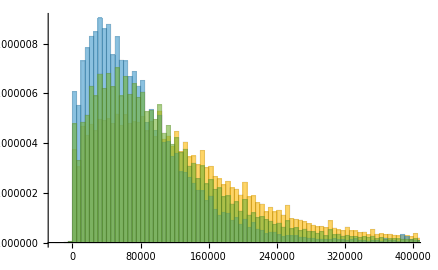

```mathematica
Histogram[
incomeWeightedData[#,"HINCP"]&/@GroupBy[Discard[allIncome,#HINCP===-60000&],#state&][[{
Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]],
Entity["AdministrativeDivision",{"Alabama","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]],
=[Illinois][EntityProperty["AdministrativeDivision","FIPSCode"]]
}]],
{5000},
"PDF"
]
```

### Income distribution over time

```mathematica
householdIncomeWeightedData[year_]:=
Enclose@Module[{t},
t=Confirm@censusQuery[
{"data",year,"acs","acs1","pums"},
{
"get"->StringRiffle[{"WGTP","HINCP"},","],
"for"->"state:*"
}
];
t=CastColumns[t,{"WGTP","HINCP"}->"Integer"];
t=Discard[t,#HINCP===-60000&];
WeightedData[Normal@t[[All,"HINCP"]],Normal@t[[All,"WGTP"]]]
]
```

```mathematica
yearIncomeDistributions=<|Echo@DateObject[{#}]->householdIncomeWeightedData[IntegerString[#]]&/@Complement[Range[2006,2024],{2020}]|>;//EchoTiming
```

Year: 2006

Year: 2007

Year: 2008

Year: 2009

Year: 2010

Year: 2011

Year: 2012

Year: 2013

Year: 2014

Year: 2015

Year: 2016

Year: 2017

Year: 2018

Year: 2019

Year: 2021

Year: 2022

Year: 2023

Year: 2024

450.903

```mathematica
KeyDropFrom[yearIncomeDistributions,{DateObject[{2007}],DateObject[{2016}]}];
```

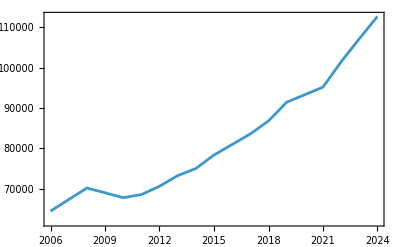

```mathematica
DateListPlot[Mean/@yearIncomeDistributions]
```

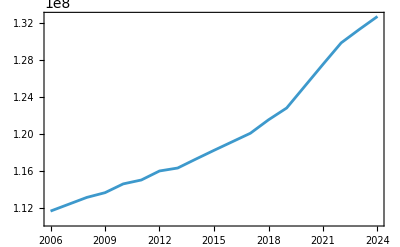

```mathematica
DateListPlot[Total[#["Weights"]]&/@yearIncomeDistributions]
```

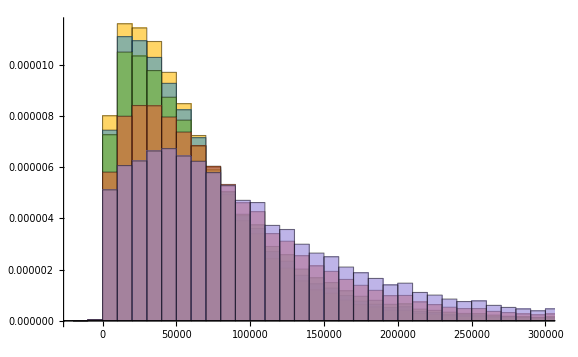

```mathematica
Histogram[{
yearIncomeDistributions[DateObject[{2006}]],
yearIncomeDistributions[DateObject[{2009}]],
yearIncomeDistributions[DateObject[{2014}]],
yearIncomeDistributions[DateObject[{2019}]],
yearIncomeDistributions[DateObject[{2024}]]
},
{10000},
"PDF"
]
```

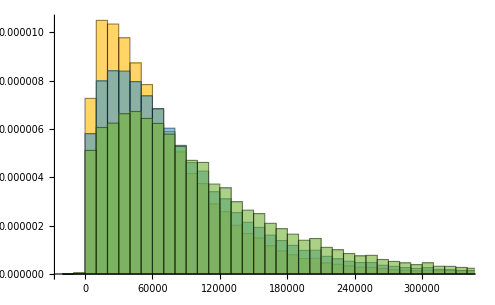

```mathematica
Histogram[{
yearIncomeDistributions[DateObject[{2014}]],
yearIncomeDistributions[DateObject[{2019}]],
yearIncomeDistributions[DateObject[{2024}]]
},
{10000},
"PDF"
]
```

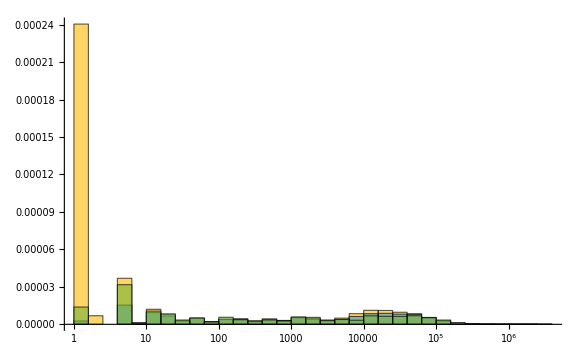

```mathematica
Histogram[{
yearIncomeDistributions[DateObject[{2014}]],
yearIncomeDistributions[DateObject[{2019}]],
yearIncomeDistributions[DateObject[{2024}]]
},
{"Log",Automatic},
"PDF"
]
```

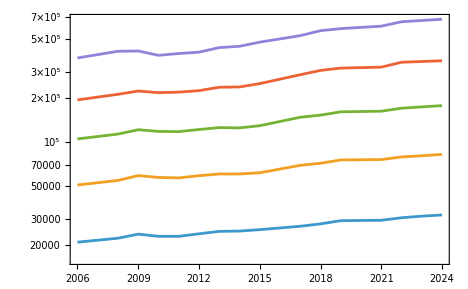

```mathematica
DateListLogPlot[
AssociationThread[Keys[yearIncomeDistributions],#]&/@Transpose@Values[Quantile[#,{0.1,0.25,0.5,0.75,0.9}]&/@yearIncomeDistributions]
]
```

```mathematica
(*From ChatGPT*)
gini[x_List]:=With[{xs=Sort[x],n=Length[x]},(2 Range[n].xs)/(n Total[x])-(n+1)/n]
gini2[wd_WeightedData]:=Module[{x=wd["InputData"],w=wd["Weights"],ord,xs,ws,W,Y,p,L,area},ord=Ordering[x];
xs=x[[ord]];
ws=w[[ord]];
W=Total[ws];
Y=Total[ws xs];
If[W==0||Y==0,Return[Indeterminate]];
(*Lorenz curve points*)p=Prepend[Accumulate[ws]/W,0];(*cumulative population share*)L=Prepend[Accumulate[ws xs]/Y,0];(*cumulative income share*)(*trapezoid area under Lorenz curve,vectorized*)area=Total[MovingAverage[L,2]*Differences[p]];
1-2 area]
```

```mathematica
gini[N@yearIncomeDistributions[DateObject[{2024}]]["InputData"]]
```

0.479824

```mathematica
gini2[N@yearIncomeDistributions[DateObject[{2024}]]]
```

0.479664

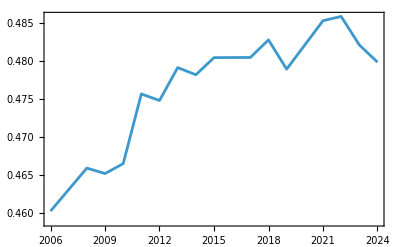

```mathematica
DateListPlot[gini[N@#["InputData"]]&/@yearIncomeDistributions]
```

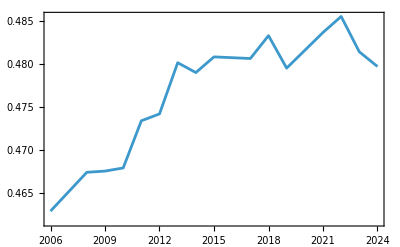

```mathematica
DateListPlot[gini2[N@#]&/@yearIncomeDistributions,PlotRange->All]
```

```mathematica
Comap[{Mean,StandardDeviation}]@Module[{wd=#,data,weights},
{data,weights}=Transpose@Select[Transpose[{wd["InputData"],wd["Weights"]}],#[[1]]>0&];
WeightedData[Log@N@data,weights]
]&/@yearIncomeDistributions
```

<|Year: 2006→{10.669,0.997039},Year: 2008→{10.7497,0.995908},Year: 2009→{10.7341,0.997249},Year: 2010→{10.7205,0.996836},Year: 2011→{10.7221,1.01112},Year: 2012→{10.7497,1.01336},Year: 2013→{10.7746,1.0305},Year: 2014→{10.8006,1.02786},Year: 2015→{10.8438,1.02149},Year: 2017→{10.9073,1.02451},Year: 2018→{10.9384,1.02927},Year: 2019→{10.9939,1.02675},Year: 2021→{11.02,1.06457},Year: 2022→{11.0792,1.0674},Year: 2023→{11.1394,1.06597},Year: 2024→{11.1908,1.06956}|>